## Setup adaptive dynamics commands (select and run this cell first)

## Setup

```mathematica
Off[General::spell];
Off[General::spell1];
Off[NIntegrate::"slwcon"];
```

```mathematica
<<LinearAlgebra`
<<Statistics`
<<NumericalMath`
<<Graphics`
```

General::obspkg: "LinearAlgebra`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::obspkg: "Statistics`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::newpkg: "Statistics`ClusterAnalysis`" is now available as the "Hierarchical Clustering Package". See the Compatibility Guide for updating information.

General::obspkg: "Statistics`ContinuousDistributions`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::obspkg: "Statistics`DiscreteDistributions`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::stop: Further output of General :: obspkg will be suppressed during this calculation.

General::obspkg: "NumericalMath`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::obspkg: "Graphics`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

## Constants

```mathematica
$tmax=1000;
$tint=500;
$popmin=10^-10;
$maxiterations=100;
$roundofftolerance=10^(-7);
```

## Default Options

```mathematica
SetOptions[NDSolve,MaxSteps->Infinity,AccuracyGoal->16];
SetOptions[NIntegrate,MaxRecursion->30,AccuracyGoal->16];
```

## Utilities

```mathematica
IntervalToPoints[int_Interval]:=Module[{nint},nint=Length[int];Return[Table[Mean[int[[i]]],{i,1,nint}]]];
```

```mathematica
DoubleDeltaDistribution/:Random[DoubleDeltaDistribution[ϵ_?NumericQ]]:=ϵ*(2*Random[Integer,{0,1}]-1);
```

```mathematica
CompoundAnd[list_]:=Module[{},And[Evaluate[Sequence@@list]]];
```

```mathematica
CompoundOr[list_]:=Module[{},Or[Evaluate[Sequence@@list]]];
```

```mathematica
AllPositiveQ[list_]:=Module[{nelements},
nelements=Length[list];
If[CompoundAnd[Table[list[[i]]>$roundofftolerance,{i,1,nelements}]],Return[True],Return[False]];
];
```

```mathematica
SelectStable[sol_,eigenvalues_]:=Module[{},
Return[Part[sol,Flatten[Position[StableQ[eigenvalues],True]]]];
];
```

```mathematica
InterpolatingFunctionQ[list_]:=Block[{},MemberQ[list[[1]],InterpolatingFunction,{0,100},Heads->True]];
```

```mathematica
ListOfNumbersQ[list_]:=Module[{ret},
If[ListQ[list]==False,ret=False,
ret=True;
Do[
If[NumberQ[list[[i]]]==False,ret=False]
,{i,1,Length[list]}];
];
Return[ret];
];
```

```mathematica
LocalMaxima[f_,{tmin_,tmax_,dt_}]:=Module[{maxs,xl,xm,xr,maxflag,tleft},

maxs={};
xm=Evaluate[f[tmin-dt]];
xr=Evaluate[f[tmin]];
maxflag=False;
Do[
xl=xm;
xm=xr;
xr=Evaluate[f[t+dt]];
If[(xl<xm)&&(xr<xm),maxs=Append[maxs,{t,xm}]];
If[(xl<xm)&&(xm==xr),maxflag=True;tleft=t];
If[(xl==xm)&&(xr<xm)&&maxflag,maxs=Append[maxs,{(t+tleft)/2,xm}];maxflag=False];
,{t,tmin,tmax-dt,dt}];

Return[Union[Round[maxs*1000]/1000.]]];
```

```mathematica
(* modified from M.Kulenovic and O.Merino's "Dynamica" *)

MinimalPeriod[orb_,eps_:$MachineEpsilon]:=Module[{flag,i,k,flag2},
flag=False;
i=0;
While[i<Length[orb]-1&&flag==False,i++;
k=i+1;
flag2=True;
While[flag2&&k≤Length[orb]-3,
If[CompoundAnd[Table[Max[Abs[orb[[i+j]]-orb[[k+j]]]]<eps,{j,0,3}]],flag2=False,k++];
];(*end while*)
flag=TrueQ[k≤Length[orb]]&&Not[flag2];
];(*end while*)

Return[If[i<Length[orb]-1,k-i,0]]];
```

```mathematica
MinimalPeriod[{1,2,1,2,1,2,1,3,1,3}]
```

2

```mathematica
Period[sol_,dt_Real:0.1,eps_Real:0.1,tol_Real:0.2,opts___?OptionQ]:=Module[{list,tmax,maxperiod,period},

tmax=sol[[1,2,1,1,2]]; (* extract tmax from interpolating function *)
list=LocalMaxima[n[1]/.sol[[1]],{Max[0.1,tmax-$tint],tmax,dt}];

(* Print["list:",list]; *)

maxperiod=MinimalPeriod[Table[list[[t,2]],{t,1,Length[list]}],eps];

(* Print["maxperiod:",maxperiod]; *)

If[Length[list]>1,
period=If[Abs[list[[Length[list],1]]-list[[Length[list]-maxperiod,1]]-(list[[Length[list]-1,1]]-list[[Length[list]-maxperiod-1,1]])]<tol,list[[Length[list],1]]-list[[Length[list]-maxperiod,1]],-42];,
(* else *)
period=-77];

Return [period]];
```

```mathematica
Period2[sol_,dt_:0.1,eps_:0.1,tol_:0.2]:=Module[{list,tmax,maxperiod,period},

tmax=sol[[1,1,2,1,1,2]]; (* extract tmax from interpolating function *)
Print[{tmax-$tint,tmax,dt}];
list=Table[{t,n[1][t]/.sol[[1]]},{t,tmax-$tint,tmax,dt}];

Print["list:",list];

maxperiod=MinimalPeriod[Table[list[[t,2]],{t,1,Length[list]}],eps];

Print["maxperiod:",maxperiod];

If[Length[list]>1,
period=If[Abs[list[[Length[list],1]]-list[[Length[list]-maxperiod,1]]-(list[[Length[list]-1,1]]-list[[Length[list]-maxperiod-1,1]])]<tol,list[[Length[list],1]]-list[[Length[list]-maxperiod,1]],-42];,
(* else *)
period=-77];

Return [period]];
```

## SelectValid

```mathematica
SelectValid[{{{g_Symbol}},{{{pop_Symbol,popmin_,popmax_}}},{{{trait_Symbol,traitmin_,traitmax_}}}},sol_]:=Module[{},
Select[sol,CompoundAnd[Table[popmax+$roundofftolerance≥#[[x,2]]≥popmin-$roundofftolerance,{x,1,Length[#]}]]&]];
```

```mathematica
SelectValid::usage="SelectValid[model, sol] picks out feasible solutions based on the range of allowable pop values in model.";
```

## Grid

```mathematica
Grid[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},nsp_Integer,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,includeendpoints},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[Grid]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[Grid]}]];
If[verboseall,verbose=True];
includeendpoints=Evaluate[IncludeEndpoints/.Flatten[{opts,Options[Grid]}]];


If[includeendpoints==True,
Return[Table[traitmin+(traitmax-traitmin)*(i-1)/(nsp-1),{i,1,nsp}]]];
If[includeendpoints==False,Return[Table[traitmin+(traitmax-traitmin)*i/(nsp+1),{i,1,nsp}]]];
];

Options[Grid]={Verbose->False,VerboseAll->False,IncludeEndpoints->False};
```

SetDelayed::write: Tag Grid in Grid[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_, traitmax_}}}}, nsp_Integer, opts___ ? OptionQ] is Protected.

Set::write: Tag Grid in Options[Grid] is Protected.

```mathematica
Grid::usage="Grid[model, nsp] returns a uniformly spaced list of trait values between traitmin and traitmax.";
```

## EcoSim

```mathematica
EcoSim[{{{g_Symbol}},{{{pop_Symbol,popmin_,popmax_}}},{{{trait_Symbol,traitmin_,traitmax_}}}},traitin_List,popics_List,tmax_?NumberQ,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,im,ndsolveopts,
(* other variables *)
traitvalues,eqns,ics,unks,sol},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{pop,popmin,popmax}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[EcoSim]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[EcoSim]}]];
If[verboseall,verbose=True];
im=Evaluate[Immigration/.Flatten[{opts,Options[EcoSim]}]];
ndsolveopts=Evaluate[NDSolveOpts/.Flatten[{opts,Options[EcoSim]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* set up eqns, ics & unks *)

eqns=Table[
pop[i]'[t]==g[i]+im
,{i,1,nsp}];

ics=Table[
pop[i][0]==popics[[i]]
,{i,1,nsp}];

unks=Table[pop[i],{i,1,nsp}];


(* solve it *)

sol=NDSolve[Flatten[Join[eqns,ics]/.Table[trait[j]->traitvalues[[j]],{j,1,nsp}]],unks,{t,0,tmax},Evaluate[Sequence@@ndsolveopts]];

Return[sol];
]];

Options[EcoSim]={Verbose->False,VerboseAll->False,Immigration->0,NDSolveOpts->{}};
```

```mathematica
EcoSim::usage="EcoSim[model, traitvalues, popics, tmax] simulates the ecological interaction  with values of trait given in the list traitvalues, subject to initial densities in list popics, from time t=0 to tmax.";
```

## SolveEcoEq

```mathematica
SolveEcoEq[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,
(* other variables *)
traitvalues,eqns,unks,sol},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[SolveEcoEq]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[SolveEcoEq]}]];
If[verboseall,verbose=True];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* set up eqns and unks *)

eqns=Table[
0==g[i]/.Table[pop[i][t]->pop[i],{i,1,nsp}]
,{i,1,nsp}];

unks=Table[pop[i],{i,1,nsp}];


(* solve it *)

sol=Solve[eqns/.Table[trait[i]->traitvalues[[i]],{i,1,nsp}],unks];


(* return answer *)

Return[sol];

]];

Options[SolveEcoEq]={Verbose->False,VerboseAll->False};
```

```mathematica
SolveEcoEq::usage="SolveEcoEq[model, traitvalues] uses Solve to solve for the equilibria of the ecological model with trait values traitvalues.";
```

## NSolveEcoEq

```mathematica
NSolveEcoEq[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,
(* other variables *)
eqns,unks,sol},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[NSolveEcoEq]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[NSolveEcoEq]}]];
If[verboseall,verbose=True];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* set up eqns and unks *)

eqns=Table[
0==g[i]/.Table[pop[i][t]->pop[i],{i,1,nsp}]
,{i,1,nsp}];

unks=Table[pop[i],{i,1,nsp}];


(* solve it *)

sol=NSolve[eqns/.Table[trait[i]->traitvalues[[i]],{i,1,nsp}],unks];

(* return answer *)

Return[sol];

]];

Options[NSolveEcoEq]={Verbose->False,VerboseAll->False};
```

```mathematica
NSolveEcoEq::usage="NSolveEcoEq[model, traitvalues] uses NSolve to solve for the equilibria of the ecological model with trait values traitvalues.";
```

## FindEcoEq

```mathematica
FindEcoEq[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,popics_List,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,findrootopts,
(* other variables *)
traitvalues,eqns,unks,sol},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[FindEcoEq]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[FindEcoEq]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[FindEcoEq]}]];
findrootopts=Evaluate[FindRootOpts/.Flatten[{opts,Options[FindEcoEq]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* set up eqns & unks *)

eqns=Table[
0==g[i]/.Table[pop[i][t]->pop[i],{i,1,nsp}]
,{i,1,nsp}];

Which[
method=="Newton",
unks=Table[{pop[i],popics[[i]],0,Infinity},{i,1,nsp}];,
method=="Secant",
unks=Table[{pop[i],popics[[i]],popics[[i]]+0.001,0,Infinity},{i,1,nsp}];,
(* else *)
True,
unks=Table[{pop[i],popics[[i]],0,Infinity},{i,1,nsp}];Message[FindEcoEq::"bdmtd",method];
];


(* solve it*)

sol=FindRoot[eqns/.Table[trait[j]->traitvalues[[j]],{j,1,nsp}],unks,Evaluate[Sequence@@findrootopts]];


(* return answer *)

Return[sol];

]];

Options[FindEcoEq]={Verbose->False,VerboseAll->False,Method->"Newton",FindRootOpts->{}};
```

```mathematica
FindEcoEq::usage="FindEcoEq[model, traitvalues, popics] uses FindRoot to solve for an equilibrium of the ecological model with trait values traitvalues, starting with initial guess popics.";
```

```mathematica
FindEcoEq::bdmtd="Unknown method `1`, using Newton's method instead.";
```

## EcoEigenvalues

```mathematica
EcoEigenvalues[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,sol_,opts___?OptionQ]:=

Module[{
(* options *)
verbose,verboseall,
(* other variables *)
traitvalues,jmat},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[EcoEigenvalues]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[EcoEigenvalues]}]];
If[verboseall,verbose=True];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* set up jacobian in one block *)

jmat=Table[D[g[i]/.Table[pop[i][t]->pop[i],{i,1,nsp}],pop[j]]/.Table[trait[j]->traitvalues[[j]],{j,1,nsp}],{i,1,nsp},{j,1,nsp}];


(* calculate eigenvalues *)

If[MatrixQ[sol],
Return[Table[Eigenvalues[jmat/.sol[[j]]],{j,1,Length[sol]}]],
Return[Eigenvalues[jmat/.sol]];
];

]];

Options[EcoEigenvalues]={Verbose->False,VerboseAll->False};
```

```mathematica
EcoEigenvalues::usage="EcoEigenvalues[model, traitvalues, sol] returns a list of eigenvalues of the Jacobian matrix of population equations with traits in list traitvalues evaluated at sol.";
```

## StableQ

```mathematica
StableQ[eigenvalues_]:=

Module[{tmp},

If[MatrixQ[eigenvalues],
tmp=Table[Which [Max[Re[eigenvalues[[i]]]]<0,True,Max[Re[eigenvalues[[i]]]]==0,Indeterminate,Max[Re[eigenvalues[[i]]]]>0,False],{i,1,Length[eigenvalues]}],
tmp=Which [Max[Re[eigenvalues]]<0,True,Max[Re[eigenvalues]]==0,Indeterminate,Max[Re[eigenvalues]]>0,False];
];
Return[tmp];
];
```

```mathematica
StableQ::usage="StableQ[eigenvalues] returns True, False, or Indeterminate for the linear stability of an equilibrium with a set of eigenvalues.";
```

## FindEcoAttractor

```mathematica
FindEcoAttractor[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,popics_List,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,ecosimopts,
(* other variables *)
tmax,tmp,tmp2,evs,sol,done},
Block[{nsp,pop,trait,traitvalues},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[FindEcoAttractor]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[FindEcoAttractor]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[FindEcoAttractor]}]];
ecosimopts=Evaluate[EcoSimOpts/.Flatten[{opts,Options[FindEcoAttractor]}]];

(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* run down list of methods *)

done=False;

Do[
If[done,Break[]];

(* method SolveEcoEq *)

If[method[[i]]=="SolveEcoEq",
If[verbose,Print["FindEcoAttractor: SolveEcoEq selected"]];
tmp=SolveEcoEq[model,traitvalues,VerboseAll->verboseall];
tmp2=SelectValid[model,tmp];
evs=EcoEigenvalues[model,traitvalues,tmp2,VerboseAll->verboseall];
sol=SelectStable[tmp2,evs];
If[verbose,
Print["FindEcoAttractor: all eq=",tmp];
Print["FindEcoAttractor: valid eq=",tmp2];
Print["FindEcoAttractor: eigenvalues=",evs];
Print["FindEcoAttractor: stable eq=",sol];
];
If[Length[sol]==0,Message[FindEcoAttractor::nosteq,traitvalues]];
If[Length[sol]==1,done=True];
If[Length[sol]==2,Message[FindEcoAttractor::musteq,Length[sol],traitvalues]];
];


(* method NSolveEcoEq *)

If[method[[i]]=="NSolveEcoEq",
If[verbose,Print["FindEcoAttractor: NSolveEcoEq selected"]];
tmp=NSolveEcoEq[model,traitvalues,VerboseAll->verboseall];
tmp2=SelectValid[model,tmp];
evs=EcoEigenvalues[model,traitvalues,tmp2,VerboseAll->verboseall];
sol=SelectStable[tmp2,evs];
If[verbose,
Print["FindEcoAttractor: all eq=",tmp];
Print["FindEcoAttractor: valid eq=",tmp2];
Print["FindEcoAttractor: eigenvalues=",evs];
Print["FindEcoAttractor: stable eq=",sol];
];
If[Length[sol]==0,Message[FindEcoAttractor::nosteq,traitvalues]];
If[Length[sol]==1,done=True];
If[Length[sol]==2,Message[FindEcoAttractor::musteq,Length[sol],traitvalues]];
];


(* method FindEcoEq *)

If[method[[i]]=="FindEcoEq",
If[verbose,Print["FindEcoAttractor: FindEcoEq selected"]];
tmp=FindEcoEq[model,traitvalues,popics,VerboseAll->verboseall];
tmp2=SelectValid[model,tmp];
evs=EcoEigenvalues[model,traitvalues,tmp2,VerboseAll->verboseall];
sol=SelectStable[tmp2,evs];
If[verbose,
Print["FindEcoAttractor: all eq=",tmp];
Print["FindEcoAttractor: valid eq=",tmp2];
Print["FindEcoAttractor: eigenvalues=",evs];
Print["FindEcoAttractor: stable eq=",sol];
];
If[Length[sol]==0,Message[FindEcoAttractor::nosteq,traitvalues]];
If[Length[sol]==1,done=True];
];


(* method EcoSim *)

If[(Length[method[[i]]]==2)&&(method[[i,1]]=="EcoSim"),
tmax=method[[i,2]];
If[verbose,Print["FindEcoAttractor: EcoSim selected"]];
sol=EcoSim[model,traitvalues,popics,tmax,Evaluate[Sequence@@ecosimopts],VerboseAll->verboseall];
done=True;
];
,{i,1,Length[method]}];

If[done,Return[sol[[1]]]];
]];

Options[FindEcoAttractor]={Verbose->False,VerboseAll->False,Method->{"SolveEcoEq",{"EcoSim",$tmax}},EcoSimOpts->{}};
```

```mathematica
FindEcoAttractor::nosteq="Warning: no stable equilibrium with traits `1`.  Resorting to numerical solution.";
```

```mathematica
FindEcoAttractor::musteq="Warning: `1` stable equilibria with traits `2`.  Resorting to numerical solution.";
```

```mathematica
FindEcoAttractor::usage="FindEcoAttractor[model, traitvalues, popics] uses a series of techniques to find for an attractor (stable equilibrium, limit cycle, strange attractor, or heteroclinic cycle) of the ecological model with trait values traitvalues, starting with initial guess popics (Method EcoSim).";
```

## Inv

```mathematica
Inv[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,sol_,traitinv_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,nintegrateopts,
(* other variables *)
tmax,tmp,tint},
Block[{nsp,pop,trait,traitvalues},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[Inv]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[Inv]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[Inv]}]];
nintegrateopts=Evaluate[NIntegrateOpts/.Flatten[{opts,Options[Inv]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* method Automatic ... if given an InterpolatingFunction, integrate from tmax-$tint to tmax.  if given replacement rules, just plug in *)

If[method=="Automatic",
If[InterpolatingFunctionQ[sol]==True,
tmax=sol[[1,2,1,1,2]]; (* extract tmax from InterpolatingFunction *)
tmp=NIntegrate[Evaluate[(g[nsp+1]/pop[nsp+1][t])/.sol/.Table[trait[j]->traitvalues[[j]],{j,1,nsp}]/.pop[nsp+1]->0/.trait[nsp+1]->traitinv],{t,Max[0,tmax-$tint],tmax},Evaluate[Sequence@@nintegrateopts]]/Min[$tint,tmax];,
 (* else *)
tmp=(g[nsp+1]/pop[nsp+1][t])/.Table[pop[i][t]->pop[i],{i,1,nsp}]/.sol/.Table[trait[j]->traitvalues[[j]],{j,1,nsp}]/.pop[nsp+1]->0/.trait[nsp+1]->traitinv;
];
];


(* method Periodic ... integrate from tmax-tint (user supplied) to tmax *)

 If[Length[method]==2,If[method[[1]]=="Periodic",
If[InterpolatingFunctionQ[sol]==True,
tint=method[[2]];
tmax=sol[[1,2,1,1,2]]; (* extract tmax from interpolating function *)
tmp=NIntegrate[Evaluate[(g[nsp+1]/pop[nsp+1][t])/.sol/.Table[trait[j]->traitvalues[[j]],{j,1,nsp}]/.pop[nsp+1]->0/.trait[nsp+1]->traitinv],{t,Max[0,tmax-tint],tmax},Evaluate[Sequence@@nintegrateopts]]/Min[tint,tmax];,
 (* else *)
tmp=(g[nsp+1]/pop[nsp+1][t])/.Table[pop[i][t]->pop[i],{i,1,nsp}]/.sol/.Table[trait[j]->traitvalues[[j]],{j,1,nsp}]/.pop[nsp+1]->0/.trait[nsp+1]->traitinv;
];
];
];


(* method Equilibrium ... take last value of an InterpolatingFunction *)

If[method=="Equilibrium",
tmax=sol[[1,2,1,1,2]]; (* extract tmax from InterpolatingFunction *)
tmp=Evaluate[(g[nsp+1]/pop[nsp+1][t])/.sol/.Table[trait[j]->traitvalues[[j]],{j,1,nsp}]/.pop[nsp+1]->0/.trait[nsp+1]->traitinv/.t->tmax];
];

If[verbose,Print["Inv: inv=",Evaluate[tmp]]];
Return[tmp];
]];

Options[Inv]={Verbose->False,VerboseAll->False,Method->"Automatic",NIntegrateOpts->{}};
```

```mathematica
Inv::usage="Inv[model, traitvalues, sol, traitinv] calculates the rate an invader with value of traitinv of a trait named trait invades a community at densities of pop given by sol and trait values traitvalues, given fitness function g.";
```

## FitnessGradient

```mathematica
FitnessGradient[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,sol_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,invopts,
(* other variables *)
tmp,ϵ,traitvalues},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[FitnessGradient]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[FitnessGradient]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[FitnessGradient]}]];
invopts=Evaluate[InvOpts/.Flatten[{opts,Options[FitnessGradient]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* continuous method *)

If[method=="Continuous",
tmp=Table[D[Inv[model,traitvalues,sol,traitinv,Evaluate[Sequence@@invopts],VerboseAll->verboseall],traitinv]/.traitinv->traitvalues[[j]],{j,1,nsp}];
];


(* twopoint method *)

If[MemberQ[method,"TwoPoint"],
ϵ=Evaluate[Method/.{opts}][[2]];
tmp=Table[
(Inv[model,traitvalues,sol,traitvalues[[j]]+ϵ/2,Evaluate[Sequence@@invopts],VerboseAll->verboseall]-Inv[model,traitvalues,sol,traitvalues[[j]]-ϵ/2,Evaluate[Sequence@@invopts],VerboseAll->verboseall])/ϵ/.Table[trait[i]->traitvalues[[i]],{i,1,nsp}],{j,1,nsp}];
];


(* lefthand method *)

If[MemberQ[method,"LeftHand"],
ϵ=Evaluate[Method/.{opts}][[2]];
tmp=Table[-Inv[model,traitvalues,sol,traitvalues[[j]]-ϵ,Evaluate[Sequence@@invopts],VerboseAll->verboseall]/ϵ/.Table[trait[i]->traitvalues[[i]],{i,1,nsp}],{j,1,nsp}];
];


(* righthand method *)

If[MemberQ[method,"RightHand"],
ϵ=Evaluate[Method/.{opts}][[2]];
tmp=Table[Inv[model,traitvalues,sol,traitvalues[[j]]+ϵ,Evaluate[Sequence@@invopts],VerboseAll->verboseall]/ϵ/.Table[trait[i]->traitvalues[[i]],{i,1,nsp}],{j,1,nsp}];
];


(* return answer *)

Return[tmp];

]];

Options[FitnessGradient]={Verbose->False,VerboseAll->False,Method->"Continuous",InvOpts->{}};
```

```mathematica
FitnessGradient::usage="FitnessGradient[model, traitvalues, sol] returns the slopes of the invader fitness function evaluated with population densities sol at each trait value in traitvalues.";
```

## SolveSingularStrategies

```mathematica
SolveSingularStrategies[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},sol_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,fitnessgradientopts,
(* other variables *)
fg},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[SolveSingularStrategies]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[SolveSingularStrategies]}]];
If[verboseall,verbose=True];
fitnessgradientopts=Evaluate[FitnessGradientOpts/.Flatten[{opts,Options[SolveSingularStrategies]}]];

(* figure out number of species *)

nsp=Count[sol,pop[_]->_,2];


(* compute FitnessGradient *)

fg=FitnessGradient[model,Table[trait[i],{i,1,nsp}],Evaluate[sol],Evaluate[Sequence@@fitnessgradientopts],VerboseAll->verboseall];
If[verbose,Print["SolveSingularStrategies: fitnessgradient=",fg]];
Return[Solve[Table[fg[[i]]==0,{i,1,nsp}],Table[trait[i],{i,1,nsp}]]];

]];

Options[SolveSingularStrategies]={Verbose->False,VerboseAll->False,FitnessGradientOpts->{}};
```

```mathematica
SolveSingularStrategies::usage="SolveSingularStrategies[model, sol] uses Solve to solve for singular strategies, where sol is an algebraic replacement rule giving an equilibrium.";
```

## NSolveSingularStrategies

```mathematica
NSolveSingularStrategies[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},sol_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,fitnessgradientopts,
(* other variables *)
fg},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[NSolveSingularStrategies]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[NSolveSingularStrategies]}]];
If[verboseall,verbose=True];
fitnessgradientopts=Evaluate[FitnessGradientOpts/.Flatten[{opts,Options[NSolveSingularStrategies]}]];

(* figure out number of species *)

nsp=Count[sol,pop[_]->_,2];


(* compute FitnessGradient *)

fg=FitnessGradient[model,Table[trait[i],{i,1,nsp}],Evaluate[sol],Evaluate[Sequence@@fitnessgradientopts],VerboseAll->verboseall];
If[verbose,Print["SolveSingularStrategies: fitnessgradient=",fg]];
Return[NSolve[Table[fg[[i]]==0,{i,1,nsp}],Table[trait[i],{i,1,nsp}]]];

]];

Options[NSolveSingularStrategies]={Verbose->False,VerboseAll->False,FitnessGradientOpts->{}};
```

```mathematica
NSolveSingularStrategies::usage="NSolveSingularStrategies[model, sol] uses Solve to solve for singular strategies, where sol is an algebraic replacement rule giving an equilibrium.";
```

## FindSingularStrategy

```mathematica
FindSingularStrategy[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,popics_List,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,fitnessgradientopts,findecoattractoropts,findrootopts,
(* other variables *)
traitics,traitrange,evunks,sol,fg},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};
traitrange=traitmax-traitmin;


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[FindSingularStrategy]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[FindSingularStrategy]}]];
If[verboseall,verbose=True];
fitnessgradientopts=Evaluate[FitnessGradientOpts/.Flatten[{opts,Options[FindSingularStrategy]}]];
findecoattractoropts=Evaluate[FindEcoAttractorOpts/.Flatten[{opts,Options[FindSingularStrategy]}]];
findrootopts=Evaluate[FindRootOpts/.Flatten[{opts,Options[FindSingularStrategy]}]];
method=Evaluate[Method/.Flatten[{opts,Options[FindSingularStrategy]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitics=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitics=traitin,
(* really, else! *)
traitics=traitin;
];


(* set up evunks *)

Which[
method=="Newton",evunks=Table[{trait[i],traitics[[i]],traitmin,traitmax},{i,1,nsp}];,
method=="Secant",evunks=Table[{trait[i],traitics[[i]],traitics[[i]]+0.001*traitrange,traitmin,traitmax},{i,1,nsp}];,
(* else *)
True,evunks=Table[{trait[i],traitics[[i]],traitics[[i]]+0.001*traitrange,traitmin,traitmax},{i,1,nsp}];Message[FindSingularStrategy::"bdmtd",method];
];


(* findroot this: *)

thing[traitvalues_?ListOfNumbersQ]:=Module[{},
$numiter++;
If[verbose,Print["FindSingularStrategy: iteration=",$numiter,", traitvalues=",traitvalues]];
sol=FindEcoAttractor[model,traitvalues,popics,Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
If[verbose,Print["FindSingularStrategy: sol=",sol]];
If[CompoundOr[Table[Evaluate[pop[i][t]/.sol]<$roundofftolerance,{i,1,nsp}]],
fg=Table[-2001,{i,1,nsp}],
fg=FitnessGradient[model,traitvalues,sol,Evaluate[Sequence@@fitnessgradientopts],VerboseAll->verboseall],
fg=FitnessGradient[model,traitvalues,sol, Evaluate[Sequence@@fitnessgradientopts],VerboseAll->verboseall]
];
If[verbose,Print["FindSingularStrategy: fg=",fg]];
Return[fg];
];


(* findroot *)


$numiter=0;
tmp=FindRoot[
thing[Table[trait[i],{i,1,nsp}]],Evaluate[Sequence@@evunks],Evaluate[Sequence@@findrootopts]];

Return[tmp];

]];

Options[FindSingularStrategy]={Verbose->False,VerboseAll->False,Method->"Secant",FitnessGradientOpts->{},FindEcoAttractorOpts->{},FindRootOpts->{}};
```

```mathematica
FindSingularStrategy::usage="FindSingularStrategy[model, traitics, popics] uses FindRoot to solve for a singular strategy, with initial conditions traitics and popics.";
```

```mathematica
FindSingularStrategy::bdmtd="Unknown method `1`, using Newton's method instead.";
```

## FitnessDInv2

```mathematica
FitnessDInv2[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,sol_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,invopts,
(* other variables *)
tmp},
Block[{ϵ,nsp,pop,trait,traitvalues},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[FitnessDInv2]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[FitnessDInv2]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[FitnessDInv2]}]];
invopts=Evaluate[InvOpts/.Flatten[{opts,Options[FitnessDInv2]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* continuous method *)

If[method=="Continuous",
tmp=Table[D[Inv[model,traitvalues,sol,traitinv,Evaluate[Sequence@@invopts],VerboseAll->verboseall],{traitinv,2}]/.traitinv->traitvalues[[j]]/.Table[trait[i]->traitvalues[[i]],{i,1,nsp}],{j,1,nsp}];
];


(* twopoint method *)

If[(Length[method]==2)&&(method[[1]]=="TwoPoint"),
ϵ=method[[2]];
tmp=Table[
(Inv[model,traitvalues,sol,traitvalues[[j]]+ϵ,Evaluate[Sequence@@invopts],VerboseAll->verboseall]+Inv[model,traitvalues,sol,traitvalues[[j]]-ϵ,Evaluate[Sequence@@invopts],VerboseAll->verboseall])/ϵ^2,{j,1,nsp}];
];

Return[tmp];

]];

Options[FitnessDInv2]={Verbose->False,VerboseAll->False,Method->"Continuous",InvOpts->{}};
```

```mathematica
FitnessDInv2::usage="FitnessDInv2[model, traitvalues, sol] returns a list of second derivatives of invader fitness with respect to the trait of the invader.";
```

## FitnessDRes2

```mathematica
FitnessDRes2[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,sol_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,invopts,findecoattractoropts,
(* other variables *)
ϵ,tmp,tmax,solleft,solright,popi},
Block[{nsp,pop,trait,traitvalues},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[FitnessDRes2]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[FitnessDRes2]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[FitnessDRes2]}]];
invopts=Evaluate[InvOpts/.Flatten[{opts,Options[FitnessDRes2]}]];
findecoattractoropts=Evaluate[FindEcoAttractorOpts/.Flatten[{opts,Options[FitnessDRes2]}]];

(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* continuous method *)

If[method=="Continuous",
If[NumberQ[Evaluate[n[1]/.sol]],Message[FitnessDRes2::nonsym];Return[];];
tmp=Table[D[Inv[model,Table[trait[i],{i,1,nsp}],sol,traitvalues[[j]],Evaluate[Sequence@@invopts],VerboseAll->verboseall],{trait[j],2}]/.Table[trait[i]->traitvalues[[i]],{i,1,nsp}],{j,1,nsp}];
];


(* twopoint method *)

If[MemberQ[method,"TwoPoint"],
ϵ=method[[2]];

(* get initial guess for population size *)

If[InterpolatingFunctionQ[sol]==True,
tmax=sol[[1,2,1,1,2]]; (* extract tmax from interpolating function *)
Do[
popi[i]=Evaluate[pop[i][tmax]/.sol]
,{i,1,nsp}];,
(* else *)
Do[
popi[i]=Evaluate[pop[i][t]/.sol]
,{i,1,nsp}];
];

tmp={};

Do[

(* find ecological attractors for traitres-ϵ and traitres+ϵ *)

solleft=FindEcoAttractor[model,ReplacePart[traitvalues,traitvalues[[j]]-ϵ,j],Table[ni[i],{i,1,nsp}],Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
solright=FindEcoAttractor[model,ReplacePart[traitvalues,traitvalues[[j]]+ϵ,j],Table[ni[i],{i,1,nsp}],Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];

(* calculate second derivative with finite difference *)

tmp=Append[tmp,(Inv[model,ReplacePart[traitvalues,traitvalues[[j]]+ϵ,j],solright,traitvalues[[j]],Evaluate[Sequence@@invopts],VerboseAll->verboseall]+Inv[model,ReplacePart[traitvalues,traitvalues[[j]]-ϵ,j],solleft,traitvalues[[j]],Evaluate[Sequence@@invopts],VerboseAll->verboseall])/ϵ^2];
,{j,1,nsp}];
];

Return[tmp];

]];

Options[FitnessDRes2]={Verbose->False,VerboseAll->False,Method->"Continuous",InvOpts->{},FindEcoAttractorOpts->{}};
```

```mathematica
FitnessDRes2::nonsym="FitnessDRes2 called with nonsymbolic sol.  Use Method→{\"TwoPoint\",ϵ} option.";
```

```mathematica
FitnessDRes2::usage="FitnessDRes2[model, traitvalues, sol] returns a list of second derivatives of invader fitness with respect to the trait of the resident.";
```

## ClassifySS

```mathematica
ClassifySS[fitnessdinv2_,fitnessdres2_]:=Module[{},
If[fitnessdinv2<0,Print["ESS"],Print["Non-ESS"]];
If[fitnessdres2-fitnessdinv2>0,Print["Convergence stable"],Print["Non-convergence stable"]];
If[fitnessdres2>0,Print["Singularity can spread"],Print["Singularity can't spread"]];
If[fitnessdres2+fitnessdinv2>0,Print["Nearby dimorphisms"],Print["No nearby dimorphisms"]];
];
```

```mathematica
ClassifySS::usage="ClassifySS[fitnessdinv2, fitnessdres2] classifies the singular strategy in four ways (ESS, convergence stability, singularity can spread, protected dimorphisms.";
```

## ESSQ

```mathematica
ESSQ[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,sol_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,fitnessdinv2opts,
(* other variables *)
d2,tmp},
Block[{nsp,pop,trait,traitvalues},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[ESSQ]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[ESSQ]}]];
If[verboseall,verbose=True];
fitnessdinv2opts=Evaluate[FitnessDInv2Opts/.Flatten[{opts,Options[ESSQ]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* calculate fitnessdinv2 for all strategies *)

d2=FitnessDInv2[model,traitvalues,sol/.Table[trait[i]->traitvalues[[i]],{i,1,nsp}],Evaluate[Sequence@@fitnessdinv2opts],VerboseAll->verboseall];
tmp=Table[If[d2[[i]]<0,True,False],{i,1,nsp}];
Return[tmp];
]];

Options[ESSQ]={Verbose->False,VerboseAll->False,FitnessDInv2Opts->{Method->{"TwoPoint",0.001}}};
```

```mathematica
ESSQ::usage="ESSQ[model, traitvalues, sol] checks local ESS stability for each species.";
```

## GlobalESSQ

```mathematica
GlobalESSQ[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,sol_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,tmp,nmaximizeopts,invopts,
(* other variables *)
traitinv},
Block[{nsp,pop,traitvalues},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};



(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[GlobalESSQ]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[GlobalESSQ]}]];
If[verboseall,verbose=True];
nmaximizeopts=Evaluate[NMaximizeOpts/.Flatten[{opts,Options[GlobalESSQ]}]];
invopts=Evaluate[InvOpts/.Flatten[{opts,Options[GlobalESSQ]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitvalues=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitvalues=traitin,
(* really, else! *)
traitvalues=traitin;
];


(* find max invader rate .. if > 0, then not globaless *)

tmp=NMaximize[{Inv[model,traitvalues,sol/.Table[trait[i]->traitvalues[[i]],{i,1,nsp}], traitinv,Evaluate[Sequence@@invopts],VerboseAll->verboseall],traitmin≤traitinv≤traitmax},traitinv,Evaluate[Sequence@@nmaximizeopts]];

If[verbose,Print["GlobalESSQ: NMaximize=",tmp]];
If[tmp[[1]]>$roundofftolerance,
Return[{False,tmp[[1]],traitinv/.tmp[[2]]}],
Return[{True,tmp[[1]],traitinv/.tmp[[2]]}]];
]];

Options[GlobalESSQ]={Verbose->False,VerboseAll->False,NMaximizeOpts->{},InvOpts->{}};
```

```mathematica
GlobalESSQ::usage="GlobalESSQ[model, traitvalues, sol] checks global ESS stability.";
```

## EcoEvoSim

```mathematica
EcoEvoSim[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,popics_List,μ_,tmax_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,bd,fitnessgradientopts,ndsolveopts,
(* other variables *)
traitics,fg,popeqns,traiteqns,popinitialconds,traitinitialconds,popunks,traitunks,sol},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[EcoEvoSim]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[EcoEvoSim]}]];
If[verboseall,verbose=True];
bd=Evaluate[BoundaryDetection/.Flatten[{opts,Options[EcoEvoSim]}]];
fitnessgradientopts=Evaluate[FitnessGradientOpts/.Flatten[{opts,Options[EcoEvoSim]}]];
ndsolveopts=Evaluate[NDSolveOpts/.Flatten[{opts,Options[EcoEvoSim]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitics=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitics=traitin,
(* really, else! *)
traitics=traitin;
];


(* construct equations *)

fg=FitnessGradient[model,Table[trait[i],{i,1,nsp}],Table[pop[i]->pop[i][t],{i,1,nsp}],VerboseAll->verboseall,Evaluate[Sequence@@fitnessgradientopts]]/.Table[trait[i]->trait[i][t],{i,1,nsp}];

popeqns=Table[
pop[i]'[t]==g[i]
,{i,1,nsp}];

If[bd==True,
traiteqns=Table[
trait[i]'[t]==Piecewise[{
{Max[0,μ*fg[[i]]],trait[i][t]<traitmin},{μ*fg[[i]],traitmin≤trait[i][t]≤traitmax},{Min[0,μ*fg[[i]]],trait[i][t]>traitmax}
}]
,{i,1,nsp}];
, (* else *)
traiteqns=Table[
trait[i]'[t]==μ*fg[[i]]
,{i,1,nsp}];
];

popinitialconds=Table[
pop[i][0]==popics[[i]]
,{i,1,nsp}];

traitinitialconds=Table[
trait[i][0]==traitics[[i]]
,{i,1,nsp}];

popunks=Table[pop[i][t],{i,1,nsp}];

traitunks=Table[trait[i][t],{i,1,nsp}];


(* solve it *)

sol=NDSolve[Flatten[Join[popeqns/.Table[trait[i]->trait[i][t],{i,1,nsp}],traiteqns,popinitialconds,traitinitialconds]],Head/@Join[popunks,traitunks],{t,0,tmax},MaxSteps->Infinity,Evaluate[Sequence@@ndsolveopts]];

Return[sol];
]];

Options[EcoEvoSim]={Verbose->False,VerboseAll->False,BoundaryDetection->True,NDSolveOpts->{},FitnessGradientOpts->{}};
```

```mathematica
EcoEvoSim::usage="EcoEvoSim[model, traitics, popics, μ, tmax] solves the ecological model along with the canonical equation for trait dynamics, with evolution rate μ, from t=0 to tmax.";
```

## EvoSim

```mathematica
EvoSim[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,popics_,μ_,dist_,tmax_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,timedirection,pointsize,findecoattractoropts,avgopts,invopts,
(* other variables *)
period,traitics,xplotmin,xplotmax,tt,tt1,output,sol,endpops,popavgs,popavgtot,rv,mutsp,traitinv,ginv,nsp‵,newsol,newpopavgs,w},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[EvoSim]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[EvoSim]}]];
If[verboseall,verbose=True];
timedirection=Evaluate[TimeDirection/.Flatten[{opts,Options[EvoSim]}]];
pointsize=Evaluate[PointSize/.Flatten[{opts,Options[EvoSim]}]];
findecoattractoropts=Evaluate[FindEcoAttractorOpts/.Flatten[{opts,Options[EvoSim]}]];
avgopts=Evaluate[AvgOpts/.Flatten[{opts,Options[EvoSim]}]];
invopts=Evaluate[InvOpts/.Flatten[{opts,Options[EvoSim]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitics=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitics=traitin,
(* really, else! *)
traitics=traitin;
];


(* set up *)

tt=0;
tt1=0;
output={};

xplotmin=Min[traitics];
xplotmax=Max[traitics];

Do[
trait[i]=traitics[[i]];
pop[i][0]=popics[[i]];
,{i,1,nsp}];


(* find initial eco attractor *)

sol=FindEcoAttractor[model,Table[trait[i],{i,1,nsp}],Table[pop[i][0],{i,1,nsp}],Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
popavgs=Avg[model,sol,Evaluate[Sequence@@avgopts],VerboseAll->verboseall];
popavgtot=Sum[popavgs[[i]],{i,1,nsp}];
endpops=Avg[model,sol,Method->"Equilibrium",VerboseAll->verboseall];
Do[
pop[i][0]=endpops[[i]];
,{i,1,nsp}];

If[verbose,
Print["EvoSim: t=",tt," traits=",Table[trait[i],{i,1,nsp}]," popavgs=",Table[popavgs[[i]],{i,1,nsp}]]];

(* main loop begins *)

While[tt<tmax,

(* time of new mutation *)

tt=tt+Random[ExponentialDistribution[μ*popavgtot]];


(* which species mutated? *)

rv=Random[];
mutsp=Which[Evaluate[Sequence@@Flatten[Table[{rv<Sum[popavgs[[j]],{j,1,i}]/popavgtot,i},{i,1,nsp}]]]];
traitinv=Min[Max[trait[mutsp]+Random[dist],traitmin],traitmax];


(* calculate invasion rate of new species *)

ginv=Inv[model,Table[trait[i],{i,1,nsp}],sol,traitinv,Evaluate[Sequence@@invopts],VerboseAll->verboseall];
If[verbose,Print["EvoSim: t=",tt," traitinv=",traitinv," ginv=",ginv]];


(* was invasion a success? *)

If[ginv>0, (* successful invasion *)

(* write out points *)

If[Evaluate[TimeDirection/.{opts}/.Options[EvoSim]]=="LeftToRight",
output=Append[output,Table[Rectangle[{tt1,trait[i]-w},{tt,trait[i]+w}],{i,1,nsp}]]];
If[Evaluate[TimeDirection/.{opts}/.Options[EvoSim]]=="BottomToTop",
output=Append[output,Table[Rectangle[{trait[i]-w,tt1},{trait[i]+w,tt}],{i,1,nsp}]]];


(* stash old time, increment nsp, install new species *)

tt1=tt;
nsp=nsp+1;
trait[nsp]=traitinv;


(* sort out remaining community *)

pop[nsp][0]=pop[mutsp][0]*0.01;
pop[mutsp][0]=pop[mutsp][0]*0.99;
sol=FindEcoAttractor[model,Table[trait[i],{i,1,nsp}],Table[pop[i][0],{i,1,nsp}],Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
popavgs=Avg[model,sol,Evaluate[Sequence@@avgopts],VerboseAll->verboseall];
nsp‵=0;
newsol={};
newpopavgs={};
Do[
If[popavgs[[i]]>$popmin, (* species i survives *)
nsp‵=nsp‵+1;
trait[nsp‵]=trait[i];newsol=Append[newsol,pop[nsp‵]->Evaluate[pop[i]/.sol]];(*newsol=Append[newsol,pop[nsp‵][t]->Evaluate[pop[i][t]/.sol]];*)
newpopavgs=Append[newpopavgs,popavgs[[i]]];
];
,{i,1,nsp}];
nsp=nsp‵;
sol=newsol;
popavgs=newpopavgs;
popavgtot=Sum[popavgs[[i]],{i,1,nsp}];
endpops=Avg[model,sol,Method->"Equilibrium",VerboseAll->verboseall];
Do[
pop[i][0]=endpops[[i]];
,{i,1,nsp}];

If[verbose,
Print["EvoSim: t=",tt," traits=",Table[trait[i],{i,1,nsp}]," popavgs=",Table[popavgs[[i]],{i,1,nsp}]]];

(* update plot width info *)

xplotmin=Min[Append[Table[trait[i],{i,1,nsp}],xplotmin]];
xplotmax=Max[Append[Table[trait[i],{i,1,nsp}],xplotmax]];

];

(* main loop ends *)

];


(* add last points to plot *)

If[timedirection=="LeftToRight",
output=Append[output,Table[Rectangle[{tt1,trait[i]-w},{tmax,trait[i]+w}],{i,1,nsp}]]];
If[timedirection=="BottomToTop",
output=Append[output,Table[Rectangle[{trait[i]-w,tt1},{trait[i]+w,tmax}],{i,1,nsp}]]];


(* compute point width *)

(* w=pointsize*(xplotmax-xplotmin); *)
w=pointsize;

Return[Flatten[output]];

(*

(* output graph *)

If[timedirection=="LeftToRight",
Return[Show[Graphics[output],PlotRange->{{0,tmax},All},Frame->True]]];
If[timedirection=="BottomToTop",
Return[Show[Graphics[output],PlotRange->{All,{0,tmax}},Frame->True]]];

*)

]];

Options[EvoSim]={Verbose->False,VerboseAll->False,PointSize->0.01,TimeDirection->"LeftToRight",FindEcoAttractorOpts->{},AvgOpts->{},InvOpts->{}};
```

```mathematica
EvoSim::usage="EvoSim[model, traitics, popics, μ, dist, tmax] simulates mutation-limited evolution of the model, with initial trait values traitics, population initial values popics, per capita mutation rate μ, mutations distributed according to dist, until time tmax.";
```

## FindSingularStrategyX

```mathematica
FindSingularStrategyX[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,popics_List,exclude_List,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,fitnessgradientopts,findecoattractoropts,findrootopts,
(* other variables *)
traitics,traitrange,nexclude,evunks,sol,fg},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};
traitrange=traitmax-traitmin;

(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[FindSingularStrategyX]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[FindSingularStrategyX]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[FindSingularStrategyX]}]];
fitnessgradientopts=Evaluate[FitnessGradientOpts/.Flatten[{opts,Options[FindSingularStrategyX]}]];
findecoattractoropts=Evaluate[FindEcoAttractorOpts/.Flatten[{opts,Options[FindSingularStrategyX]}]];
findrootopts=Evaluate[FindRootOpts/.Flatten[{opts,Options[FindSingularStrategyX]}]];


(* figure out number of species *)

nsp=Length[traitin];
nexclude=Length[exclude];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitics=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitics=traitin,
(* really, else! *)
traitics=traitin;
];


(* set up evunks *)

Which[
method=="Newton",evunks=Table[{trait[i],traitics[[i]],traitmin,traitmax},{i,1,nsp}];,
method=="Secant",evunks=Table[{trait[i],traitics[[i]],traitics[[i]]+0.001*traitrange,traitmin,traitmax},{i,1,nsp}];,
(* else *)
True,evunks=Table[{trait[i],traitics[[i]],traitmin,traitmax},{i,1,nsp}];Message[FindSingularStrategyX::"bdmtd",method];
];


(* findroot this: *)

thing[traitvalues_?ListOfNumbersQ]:=Module[{},
$numiter++;
If[verbose,Print["FindSingularStrategyX: iteration=",$numiter,", traitvalues=",traitvalues]];
sol=FindEcoAttractor[model,traitvalues,popics,Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
If[verbose,Print["FindSingularStrategyX: sol=",sol]];
If[CompoundOr[Table[Evaluate[pop[i][t]/.sol]<$roundofftolerance,{i,1,nsp}]],
fg=Table[-2001,{i,1,nsp}],
fg=FitnessGradient[model,traitvalues,sol, Evaluate[Sequence@@fitnessgradientopts],VerboseAll->verboseall],
fg=FitnessGradient[model,traitvalues,sol, Evaluate[Sequence@@fitnessgradientopts],VerboseAll->verboseall]
];
If[verbose,Print["FindSingularStrategyX: fg=",fg]];
Return[fg/Product[Norm[traitvalues-Table[exclude[[j,i]],{i,1,nsp}]]^2,{j,1,nexclude}]];
];


(* findroot *)

$numiter=0;
tmp=FindRoot[
thing[Table[trait[i],{i,1,nsp}]],Evaluate[Sequence@@evunks],Evaluate[Sequence@@findrootopts]];

Return[tmp];

]];

Options[FindSingularStrategyX]={Verbose->False,VerboseAll->False,DampingFactor->1.0,MaxIterations->$maxiterations,WorkingPrecision->MachinePrecision,Method->"Newton",FitnessGradientOpts->{},FindEcoAttractorOpts->{},FindRootOpts->{}};
```

```mathematica
FindSingularStrategyX::usage="FindSingularStrategyX[model, traitics, popics, exclude] uses FindRoot to solve for a singular strategy, with initial conditions traitics and popics, excluding strategy sets in exclude.";
```

## FindEvoAttractor

```mathematica
FindEvoAttractor[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},traitin_List,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,μ,tmax,eps,ecoevosimopts,findsingularstrategyxopts,findecoattractoropts,essqopts,globalessqopts,fitnessdinv2opts,invopts,
(* other variables *)
done,traitics,excluded,popi,traiti,globalessq,tmp,ss,sol,dplot,iplot,essq,xexclude,branchingpoint},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[FindEvoAttractor]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[FindEvoAttractor]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[FindEvoAttractor]}]];
If[(Length[method]==3)&&(method[[1]]=="EcoEvoSim"),
μ=Evaluate[Method/.Flatten[{opts,Options[FindEvoAttractor]}]][[2]];
tmax=Evaluate[Method/.Flatten[{opts,Options[FindEvoAttractor]}]][[3]];
];
eps=Evaluate[ϵ/.Flatten[{opts,Options[FindEvoAttractor]}]];
ecoevosimopts=Evaluate[EcoEvoSimOpts/.Flatten[{opts,Options[FindEvoAttractor]}]];
findsingularstrategyxopts=Evaluate[FindSingularStrategyXOpts/.Flatten[{opts,Options[FindEvoAttractor]}]];
findecoattractoropts=Evaluate[FindEcoAttractorOpts/.Flatten[{opts,Options[FindEvoAttractor]}]];
essqopts=Evaluate[ESSQOpts/.Flatten[{opts,Options[FindEvoAttractor]}]];
globalessqopts=Evaluate[GlobalESSQOpts/.Flatten[{opts,Options[FindEvoAttractor]}]];
invopts=Evaluate[InvOpts/.Flatten[{opts,Options[FindEvoAttractor]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitics=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitics=traitin,
(* really, else! *)
traitics=traitin;
];


excluded={};

Do[
popi[i]=0.1;
,{i,1,nsp}];

Do[
traiti[i]=traitics[[i]];
,{i,1,nsp}];
done=False;


(* main loop begins here *)

While[done≠True,

If[verbose,Print["FindEvoAttractor: nsp=",nsp," traiti=",Table[traiti[i],{i,1,nsp}]," popi=",Table[popi[i],{i,1,nsp}]]];


(* method EcoEvoSim *)

If[(Length[method]==3)&&(method[[1]]=="EcoEvoSim"),
tmp=EcoEvoSim[model,Table[traiti[i],{i,1,nsp}],Table[popi[i],{i,1,nsp}],μ,tmax,Evaluate[Sequence@@ecoevosimopts],VerboseAll->verboseall];
ss[nsp]=Evaluate[Table[trait[i][tmax]/.tmp[[1]],{i,1,nsp}]];
If[verbose,Print["FindEvoAttractor: ss[",nsp,"]=",ss[nsp]]];
sol[nsp]=Table[pop[i]->Evaluate[pop[i][tmax]/.tmp[[1]]],{i,1,nsp}];
If[verbose,Print["FindEvoAttractor: sol[",nsp,"]=",sol[nsp]]];
];


(* method FindSingularStrategyX *)

If[method=="FindSingularStrategyX",
tmp=FindSingularStrategyX[model,Table[traiti[i],{i,1,nsp}],Table[popi[i],{i,1,nsp}],excluded,Evaluate[Sequence@@findsingularstrategyxopts],VerboseAll->verboseall];
ss[nsp]=Table[trait[i]/.tmp,{i,1,nsp}];
If[verbose,Print["FindEvoAttractor: ss[",nsp,"]=",ss[nsp]]];
sol[nsp]=FindEcoAttractor[model,ss[nsp],Table[popi[i],{i,1,nsp}],Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
If[verbose,Print["FindEvoAttractor: sol[",nsp,"]=",sol[nsp]]]
];


If[verbose,
iplot=Plot[Inv[model,ss[nsp],sol[nsp],traitinv],{traitinv,traitmin,traitmax},Evaluate[Sequence@@invopts],DisplayFunction->Identity];
dplot=ListPlot[Table[{ss[nsp][[i]],0},{i,1,nsp}],PlotStyle->PointSize[0.025],DisplayFunction->Identity];
Show[iplot,dplot,DisplayFunction->$DisplayFunction,PlotRange->{-0.1,0.1}];
];

essq=ESSQ[{{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}},ss[nsp],sol[nsp],Evaluate[Sequence@@essqopts],VerboseAll->verboseall];
If[verbose,Print["FindEvoAttractor: ESSQ=",essq]];

branchingpoint=False;
Do[
If[essq[[i]],
traiti[i]=ss[nsp][[i]];
popi[i]=pop[i]/.sol[nsp];
xexclude[i]=trait[i];
,(* else *)
branchingpoint=True;
traiti[i]=ss[nsp][[i]]-eps;traiti[i+1]=ss[nsp][[i]]+eps;
popi[i]=pop[i]/2/.sol[nsp];popi[i+1]=pop[i]/2/.sol[nsp];
xexclude[i]=ss[nsp][[i]]; xexclude[i+1]=ss[nsp][[i]];
Do[
traiti[j+1]=ss[nsp][[j]];
popi[j+1]=pop[j]/.sol[nsp];
xexclude[j+1]=trait[j+1];
,{j,i+1,nsp}];
Break[];
];
,{i,1,nsp}];
If[!branchingpoint,
globalessq=GlobalESSQ[model,ss[nsp],sol[nsp],Evaluate[Sequence@@globalessqopts],VerboseAll->verboseall];
If[!globalessq[[1]], (* not a global ess *)
traiti[nsp+1]=globalessq[[3]];
popi[nsp+1]=0.01;
If[verbose,Print["FindEvoAttractor: Nonglobal ESS, placing invader at ",trait,"=",traiti[nsp+1]]];,
(* else .. if globaless *)
done=True;
];
];
nsp=nsp+1;
excluded={Table[xexclude[i],{i,1,nsp}]};
];

Return[ss[nsp-1]];
]];

Options[FindEvoAttractor]={Verbose->False,VerboseAll->False,Method->{"EcoEvoSim",0.1,100000},ϵ->0.01,EcoEvoSimOpts->{},FindSingularStrategyXOpts->{},FindEcoAttractorOpts->{},ESSQOpts->{},GlobalESSQOpts->{},FitnessDInv2Opts->{},InvOpts->{}};
```

```mathematica
FindEvoAttractor::usage="FindEvoAttractor[model, traitics] finds an evolutionary attractor (global ESS) with starting guess traitics.";
```

## FindBranchingPoint

```mathematica
FindBranchingPoint[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},{par_Symbol,parfirst_},traitin_List,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,findsingularstrategyopts,findecoattractoropts,fitnessdinv2opts,findrootopts,
(* other variables *)
traitics,unks,ret,thing,popics},
Block[{nsp,pop,trait,glocal},

(* set up model *)

model={{{glocal}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[FindBranchingPoint]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[FindBranchingPoint]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[FindBranchingPoint]}]];
findsingularstrategyopts=Evaluate[FindSingularStrategyOpts/.Flatten[{opts,Options[FindBranchingPoint]}]];
findecoattractoropts=Evaluate[FindEcoAttractorOpts/.Flatten[{opts,Options[FindBranchingPoint]}]];
fitnessdinv2opts=Evaluate[FitnessDInv2Opts/.Flatten[{opts,Options[FindBranchingPoint]}]];
findrootopts=Evaluate[FindRootOpts/.Flatten[{opts,Options[FindBranchingPoint]}]];


(* figure out number of species *)

nsp=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitics=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitics=traitin,
(* really, else! *)
traitics=traitin;
];


popics=Table[0.01,{i,1,nsp}];

If[verbose,Print["FindBranchingPoint: Method=",method]];

Which[
method=="Newton",unks={parvalue,parfirst};,
method=="Secant",unks={parvalue,parfirst,parfirst+0.0001};,
True,unks={parvalue,parfirst};Message[FindBranchingPoint::"bdmtd",method];
];


thing[parvalue_?NumberQ]:=Module[{ss,sol,dinv2,ret},
$numiterfbp++;
glocal[i_]:=g[i]/.par->parvalue;
If[verbose,Print["FindBranchingPoint: iteration=",$numiterfbp," ",par,":",parvalue]];
If[verbose,Print["FindBranchingPoint: traitics=",traitics]];
ss=FindSingularStrategy[model,traitics,popics,Evaluate[Sequence@@findsingularstrategyopts],VerboseAll->verboseall];
If[verbose,Print["FindBranchingPoint: ss=",ss]];
sol=FindEcoAttractor[model,ss,popics,Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
If[verbose,Print["FindBranchingPoint: sol=",sol]];
If[CompoundOr[Table[Evaluate[pop[i]/.sol]<$roundofftolerance,{i,1,nsp}]],
dinv2=Table[-2001,{i,1,nsp}],
dinv2=FitnessDInv2[model,ss,sol,Evaluate[Sequence@@fitnessdinv2opts],VerboseAll->verboseall];
];
If[verbose,Print["FindBranchingPoint: dinv2=",dinv2]];
ret=Product[dinv2[[i]],{i,1,nsp}];
If[verbose,Print["FindBranchingPoint: ret=",ret]];
Return[ret];
];

$numiterfbp=0;
tmp=FindRoot[thing[parvalue],unks,Evaluate[Sequence@@findrootopts]];

Return[parvalue/.tmp];

]];

Options[FindBranchingPoint]={Verbose->False,VerboseAll->False,Method->"Newton",FindSingularStrategyOpts->{},FindEcoAttractorOpts->{},FitnessDInv2Opts->{Method->{"TwoPoint",0.001}},FindRootOpts->{}};
```

```mathematica
FindBranchingPoint::usage="FindBranchingPoint[model, {par, parfirst}, traitics] finds a branching point using FindRoot.";
```

## PlotPIP

```mathematica
PlotPIP[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},{plotmin_,plotmax_,dtrait_},opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,findecoattractoropts,invopts,
(* other variables *)
ginv,sol,n1initial,period,tmin,tmax,tint},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[PlotPIP]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[PlotPIP]}]];
If[verboseall,verbose=True];
findecoattractoropts=Evaluate[FindEcoAttractorOpts/.Flatten[{opts,Options[PlotPIP]}]];
invopts=Evaluate[InvOpts/.Flatten[{opts,Options[PlotPIP]}]];


(* if precomputed values exist, load them *)

If[Evaluate[Input/.{opts}/.Options[PlotPIP]]==True,

Do[
Do[
ginv[traitinv,traitres]=$piptempdata[traitinv,traitres];
,{traitinv,plotmin,plotmax,dtrait}];
,{traitres,plotmin,plotmax,dtrait}];,


(* else, compute them *)

n1initial=0.01;

tmax=$tmax;

Do[
If[verbose,Print["PlotPIP: traitres=",traitres]];
sol=FindEcoAttractor[model,{traitres},{n1initial},Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
If[verbose,Print["PlotPIP: sol=",sol]];

n1initial=Evaluate[n[1][tmax]/.sol]; 

If[InterpolatingFunctionQ[sol],
period=Period[sol,VerboseAll->verboseall];
period=T;
If[verbose,Print["PlotPIP: Numerical solution, period=",period]];
If[period>0,tint=period,tint=$tint];,
(* else *)
tmax=$tmax;tint=$tint
];

gself=Inv[model,{traitres},sol,traitres,Evaluate[Sequence@@invopts],VerboseAll->verboseall];
If[verbose,Print["PlotPIP: gself=",gself]];
Do[
ginv[traitinv,traitres]=Inv[model,{traitres},sol,traitinv,Evaluate[Sequence@@invopts],VerboseAll->verboseall]-gself;
,{traitinv,plotmin,plotmax,dtrait}];
,{traitres,plotmin,plotmax,dtrait}];
];

If[Evaluate[Output/.{opts}/.Options[PlotPIP]]==True,
Do[
Do[
$piptempdata[traitinv,traitres]=ginv[traitinv,traitres];
,{traitinv,plotmin,plotmax,dtrait}]
,{traitres,plotmin,plotmax,dtrait}];
];

Return[ListDensityPlot[Table[Sign[-ginv[traitinv,traitres]],{traitinv,plotmin,plotmax,dtrait},{traitres,plotmin,plotmax,dtrait}],Mesh->False,DataRange->{{plotmin,plotmax},{plotmin,plotmax}},InterpolationOrder->0]];

]];

Options[PlotPIP]={Verbose->False,VerboseAll->False,Output->False,Input->False,FindEcoAttractorOpts->{},InvOpts->{}};
```

```mathematica
PlotPIP::usage="PlotPIP[model, {plotmin, plotmax, dtrait}] generates a pairwise invasibility plot, where the trait varies from plotmin to plotmax by dtrait.";
```

## PlotMIP

```mathematica
PlotMIP[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},{plotmin_,plotmax_,dtrait_},opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,findecoattractoropts,invopts,
(* other variables *)
ginv,sol,n1initial,period,tmin,tmax,tint},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[PlotMIP]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[PlotMIP]}]];
If[verboseall,verbose=True];
findecoattractoropts=Evaluate[FindEcoAttractorOpts/.Flatten[{opts,Options[PlotMIP]}]];
invopts=Evaluate[InvOpts/.Flatten[{opts,Options[PlotMIP]}]];


(* if precomputed values exist, load them *)

If[Evaluate[Input/.{opts}/.Options[PlotMIP]]==True,

Do[
Do[
ginv[traitinv,traitres]=$piptempdata[traitinv,traitres];
,{traitinv,plotmin,plotmax,dtrait}];
,{traitres,plotmin,plotmax,dtrait}];,


(* else, compute them *)

n1initial=0.01;

tmax=$tmax;

Do[
If[verbose,Print["PlotMIP: traitres=",traitres]];
sol=FindEcoAttractor[model,{traitres},{n1initial},Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
If[verbose,Print["PlotMIP: sol=",sol]];

n1initial=Evaluate[n[1][tmax]/.sol]; 

If[InterpolatingFunctionQ[sol],
period=Period[sol,VerboseAll->verboseall];
period=T;
If[verbose,Print["PlotMIP: Numerical solution, period=",period]];
If[period>0,tint=period,tint=$tint];,
(* else *)
tmax=$tmax;tint=$tint
];

gself=Inv[model,{traitres},sol,traitres,Evaluate[Sequence@@invopts],VerboseAll->verboseall];
If[verbose,Print["PlotMIP: gself=",gself]];
Do[
ginv[traitinv,traitres]=Inv[model,{traitres},sol,traitinv,Evaluate[Sequence@@invopts],VerboseAll->verboseall]-gself;
,{traitinv,plotmin,plotmax,dtrait}];
,{traitres,plotmin,plotmax,dtrait}];
];

If[Evaluate[Output/.{opts}/.Options[PlotMIP]]==True,
Do[
Do[
$piptempdata[traitinv,traitres]=ginv[traitinv,traitres];
,{traitinv,plotmin,plotmax,dtrait}]
,{traitres,plotmin,plotmax,dtrait}];
];

Return[ListDensityPlot[Table[Which[
(ginv[trait1,trait2]≥0)&&(ginv[trait2,trait1]≥0),0,
(ginv[trait1,trait2]≥0)&&(ginv[trait2,trait1]<0),1/3,
(ginv[trait1,trait2]<0)&&(ginv[trait2,trait1]≥0),2/3,
(ginv[trait1,trait2]<0)&&(ginv[trait2,trait1]<0),1]
,{trait2,plotmin,plotmax,dtrait},{trait1,plotmin,plotmax,dtrait}],Mesh->False,DataRange->{{plotmin,plotmax},{plotmin,plotmax}}]];

]];

Options[PlotMIP]={Verbose->False,VerboseAll->False,Output->False,Input->False,FindEcoAttractorOpts->{},InvOpts->{}};
```

```mathematica
PlotMIP::usage="PlotMIP[model, {plotmin, plotmax, dtrait}] plots the outcome of interaction between two species, where the trait varies from plotmin to plotmax by dtrait.";
```

## BifurcationData

```mathematica
BifurcationData[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},{par_Symbol,parfirst_,parlast_,dpar_},traitin_List,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,fgthreshold,findecoattractoropts,findsingularstrategyopts,essqopts,globalessqopts,
(* other variables *)
traitics,parvalue,nsp2,traiti,popi,globallystable,locallystable,unstable,ss,ssold,sol,fg,essq,globalessq,popavgs},
Block[{nsp,pop,trait,glocal},

(* set local copy of g *)

glocal[i_]:=g[i]/.par->parvalue;


(* set up model *)

model={{{glocal}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[BifurcationData]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[BifurcationData]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[BifurcationData]}]];
fgthreshold=Evaluate[FitnessGradientThreshold/.Flatten[{opts,Options[BifurcationData]}]];
findecoattractoropts=Evaluate[FindEcoAttractorOpts/.Flatten[{opts,Options[BifurcationData]}]];
findsingularstrategyopts=Evaluate[FindSingularStrategyOpts/.Flatten[{opts,Options[BifurcationData]}]];
essqopts=
Evaluate[ESSQOpts/.Flatten[{opts,Options[BifurcationData]}]];
globalessqopts=
Evaluate[GlobalESSQOpts/.Flatten[{opts,Options[BifurcationData]}]];


(* figure out number of species *)

nsp2=Length[traitin];


(* convert replacement rules to a table of numbers if need be *)

If[Head[traitin[[1]]]==Rule,
traitics=Table[trait[i]/.traitin,{i,1,nsp}],
(* else *)
traitics=traitin,
(* really, else! *)
traitics=traitin;
];


(* initialize initial conditions *)

Do[
traiti[i]=traitics[[i]];
popi[i]=0.01;
,{i,1,nsp2}];

(* set up output lists *)

globallystable={};
locallystable={};
unstable={};

(* main loop begins here *)

Do[
If[verbose,Print["BifurcationData: ",par,"=",parvalue]];
If[verbose,Print["BifurcationData: traiti=",Table[traiti[i],{i,1,nsp2}]]];
sol=FindEcoAttractor[model,Table[traiti[i],{i,1,nsp2}],Table[popi[i],{i,1,nsp2}],Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];
If[AllPositiveQ[Evaluate[Table[pop[i][t]/.sol,{i,1,nsp2}]]],(* do nothing *),
(* else *)
Message[BifurcationData::zeron,sol,Table[traiti[i],{i,1,nsp2}],par,parvalue];Goto[escapehatch];];


(* find singular strategy *)

ss[parvalue]=
FindSingularStrategy[model,Table[traiti[i],{i,1,nsp2}],Table[popi[i],{i,1,nsp2}],Evaluate[Sequence@@findsingularstrategyopts],VerboseAll->verboseall];


(* find ecological attractor *)

sol=FindEcoAttractor[model,ss[parvalue],Table[popi[i],{i,1,nsp2}],Evaluate[Sequence@@findecoattractoropts],VerboseAll->verboseall];


(* pass messages *)

If[verbose,
Print["BifurcationData: Ending fg=",FitnessGradient[model,ss[parvalue],sol,Evaluate[Sequence@@fitnessgradientopts]]]];
If[verbose, Print["BifurcationData: ",par,"=",parvalue,", $numiter=",$numiter]];
If[verbose,Print["BifurcationData: ss[",parvalue,"]=",ss[parvalue]]];
If[verbose,Print["BifurcationData: sol=",sol]];


(* check ESS quality *)

essq=ESSQ[model,ss[parvalue],sol,Evaluate[Sequence@@essqopts],VerboseAll->verboseall];
globalessq=GlobalESSQ[model,ss[parvalue],sol,Evaluate[Sequence@@globalessqopts],VerboseAll->verboseall];
If[verbose,Print["BifurcationData: ESSQ=",essq," globalessq:",globalessq]];


(* add result to the correct list *)

Which[
(CompoundAnd[essq]&&globalessq[[1]]),Do[globallystable=Append[globallystable,{parvalue,trait[i]/.ss[parvalue]}],{i,1,nsp2}];,
(CompoundAnd[essq]&&!globalessq[[1]]),Do[locallystable=Append[locallystable,{parvalue,trait[i]/.ss[parvalue]}],{i,1,nsp2}];,
!CompoundAnd[essq],
Do[unstable=Append[unstable,{parvalue,trait[i]/.ss[parvalue]}],{i,1,nsp2}];
];

(* set up initial guesses for next point *)

popavgs=Avg[model,sol,Method->"Equilibrium"];

If[method=="LinearExtrapolation",
If[parvalue==parfirst,
Do[
traiti[i]=Evaluate[trait[i]/.ss[parvalue]];
popi[i]=popavgs[[i]];
ssold[i]=Evaluate[trait[i]/.ss[parvalue]];
,{i,1,nsp2}];,
(* else *)
Do[
traiti[i]=2*Evaluate[trait[i]/.ss[parvalue]]-ssold[i];
popi[i]=popavgs[[i]];
ssold[i]=Evaluate[trait[i]/.ss[parvalue]];
,{i,1,nsp2}];
];
];

If[method=="ConstantExtrapolation",
Do[
traiti[i]=trait[i]/.ss[parvalue];
popi[i]=pop[i][t]/.sol;
,{i,1,nsp2}];
];

Label[escapehatch];

,{parvalue,parfirst,parlast,dpar}];

Return[{globallystable,locallystable,unstable}];

]];

Options[BifurcationData]={Verbose->False,VerboseAll->False,FitnessGradientThreshold->10^(-6),Method->"LinearExtrapolation",FindEcoAttractorOpts->{},FindSingularStrategyOpts->{},ESSQOpts->{},GlobalESSQOpts->{}};
```

```mathematica
BifurcationData::zeron="Zero population found among `1` with traits `2` at `3`=`4`.  Skipping.";
```

```mathematica
BifurcationData::usage="BifurcationData[model, {par, parmin, parmax, dpar}, traitics] traces a singular strategy (or coalition) as a function of par.  Output is a list of three lists: first, globally evolutionarily stable singular coalitions; second, locally (but not globally) evolutionarily stable singular coalitions; third, locally unstable singular coalitions.";
```

## PlotBifurcationData

```mathematica
PlotBifurcationData[data_List,opts___?OptionQ]:=

Module[{},

Return[MultipleListPlot[Sequence@@data,opts,Options[PlotBifurcationData]]];
];

Options[PlotBifurcationData]={SymbolShape->{PlotSymbol[Box,3],PlotSymbol[Box,3,Filled->False],PlotSymbol[Box,1]}};
```

General::obspkg: "Graphics`MultipleListPlot`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
PlotBifurcationData::usage="PlotBifurcationData[data] plots data from BifurcationData.";
```

## Avg

```mathematica
Avg[{{{g_Symbol}}, {{{pop_Symbol, popmin_, popmax_}}}, {{{trait_Symbol, traitmin_,traitmax_}}}},sol_,opts___?OptionQ]:=

Module[{model,
(* options *)
verbose,verboseall,method,
(* other variables *)
tmax,period,tint,popavg},
Block[{nsp,pop,trait},

(* set up model *)

model={{{g}},{{{pop,popmin,popmax}}},{{{trait,traitmin,traitmax}}}};


(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[Avg]}]];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[Avg]}]];
If[verboseall,verbose=True];
method=Evaluate[Method/.Flatten[{opts,Options[Avg]}]];


(* figure out number of species *)

nsp=Length[sol];


(* method Automatic... if given an InterpolatingFunction,integrate from tmax-$tint to tmax.if given replacement rules,just plug in *)

If[method=="Automatic",
If[InterpolatingFunctionQ[sol]==True,
tmax=sol[[1,2,1,1,2]];(* extract tmax from InterpolatingFunction *)
period=Period[sol,VerboseAll->verboseall];(* try to figure the period *)
If[verbose,Print["Avg: Numerical solution, period=",period]];
If[period>0,tint=period,tint=$tint];
Do[
popavg[i]=Integrate[pop[i][t]/.sol,{t,Max[0,tmax-tint],tmax}]/Min[tint,tmax];
,{i,1,nsp}];
,(* else *)
Do[
popavg[i]=pop[i]/.sol;
,{i,1,nsp}];
];
];


(* method Periodic... integrate from tmax-tint (user supplied) to tmax *)

If[Length[method]==2,If[method[[1]]=="Periodic",If[InterpolatingFunctionQ[sol]==True,
tint=method[[2]];
tmax=sol[[1,2,1,1,2]];(* extract tmax from interpolating function *)Do[
popavg[i]=Integrate[pop[i][t]/.sol,{t,Max[0,tmax-tint],tmax}]/Min[tint,tmax];
,{i,1,nsp}];
,(* else *)
Do[
popavg[i]=pop[i]/.sol;
,{i,1,nsp}];
];
];
];


(* method Equilibrium... take last value of an InterpolatingFunction*)

If[method=="Equilibrium",
If[InterpolatingFunctionQ[sol]==True,
tmax=sol[[1,2,1,1,2]];(* extract tmax from InterpolatingFunction *)
Do[
popavg[i]=pop[i][tmax]/.sol;
,{i,1,nsp}];
,(* else *)
Do[
popavg[i]=pop[i]/.sol;
,{i,1,nsp}];
];
];

Return[Table[popavg[i],{i,1,nsp}]];

]];

Options[Avg]={Verbose->False,VerboseAll->False,Method->"Automatic"};
```

```mathematica
Avg::usage="Avg[model, sol] computes the average population densities in sol, which are returned in a list.";
```

## ModelSummary

```mathematica
ModelSummary[{eqns_List,pops_List,traits_List}]:=Module[{i,j},

nguilds=Length[pops];
If[Length[eqns]≠nguilds,Print["eqns/pops mismatch"]];
Print["nguilds=",nguilds];

Do[
ncomps[i]=Length[pops[[i]]];
Do[
{comp[i,j],compmin[i,j],compmax[i,j]}=pops[[i,j]];
,{j,1,ncomps[i]}];
Print["ncomps[",i,"]=",ncomps[i]," comps[",i,"]=",Table[ToString[compmin[i,j]]<>" ≤ "<>ToString[comp[i,j]]<>" ≤ "<>ToString[compmax[i,j]],{j,1,ncomps[i]}]];
ntraits[i]=Length[traits[[i]]];
Do[
{trait[i,j],traitmin[i,j],traitmax[i,j]}=traits[[i,j]];
,{j,1,ntraits[i]}];
Print["ntraits[",i,"]=",ntraits[i]," traits[",i,"]=",Table[ToString[traitmin[i,j]]<>" ≤ "<>ToString[trait[i,j]]<>" ≤ "<>ToString[traitmax[i,j]],{j,1,ntraits[i]}]];
,{i,1,nguilds}];

];
```

## Lotka-Volterra Competition

Here we will investigate the Lotka-Volterra competition model following Geritz et al. (in Adaptive Speciation, 2004, pp. 54-75).  x is the trait, and σa is the model parameter of interest (width of the competition kernel).

Verified with adaptivedynamics v0.1, January 23, 2006 – CAK

```mathematica
Off[Solve::ratnz]
Off[RowReduce::luc]
Off[Solve::svars]
```

### First set up the model

```mathematica
g[i_]:=r*(1-Sum[a[x[i],x[j]]*n[j][t],{j,1,nsp}]/k[x[i]])*n[i][t];
a[xi_,xj_]:=E^(-0.5*(xi-xj)^2/σa^2);
k[x_]:=k0-λ*(x-x0)^2;

lv={{{g}},{{{n,0,k0}}},{{{x,-0.999,0.999}}}};
```

### Set parameters

```mathematica
σa=0.3;
k0=1;
x0=0;
λ=1;
r=1;
```

### First, simulate growth of a single species with trait x=0.5

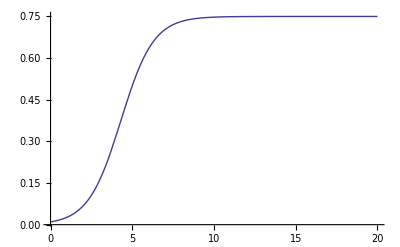

```mathematica
tmax=20;

sol=EcoSim[lv,{0.5},{0.01},tmax];
Plot[n[1][t]/.sol,{t,0,tmax},PlotRange->All]
```

### Now simulate competition between 50 species evenly spaced along the trait axis

```mathematica
tmax=100000;

nsp=50;

Do[
x[i]=2*i/(nsp+1)-1;
,{i,1,nsp}];

sol=EcoSim[lv,Table[x[i],{i,1,nsp}],Table[0.01,{i,1,nsp}],tmax];
```

#### Densities vs. time

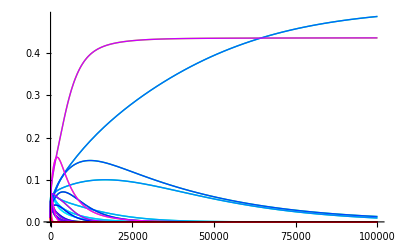

```mathematica
Plot[Evaluate[Table[n[i][t],{i,1,nsp}]/.sol],{t,0,tmax},PlotStyle->Table[Hue[i/nsp],{i,1,nsp}],PlotRange->All]
```

#### Densities vs trait

```mathematica
Animate[
ListPlot[Table[{x[i],n[i][t]/.sol[[1]]},{i,1,nsp}],PlotLabel->t,Joined->True,PlotStyle->PointSize[0.02],PlotRange->{0,0.6}]
,{t,0,tmax,tmax/100},AnimationRunning->False]
```

#### Densities vs trait vs time

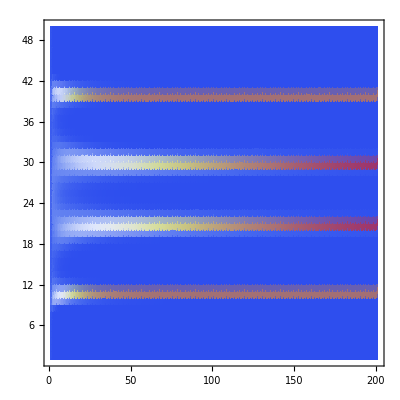

```mathematica
ListDensityPlot[Table[n[i][t]/.sol[[1]],{i,1,nsp},{t,0,tmax,tmax/200}],ColorFunction->"TemperatureMap",PlotRange->All]
```

```mathematica
Clear[x]
```

### Solving for ecological equilibria in four different ways

#### SolveEcoEq and NSolveEcoEq give all equilibria

```mathematica
SolveEcoEq[lv,{0.5}]
```

{{n[1]→0.},{n[1]→0.75}}

```mathematica
SolveEcoEq[{{{g}},{{{n,0,1}}},{{{x,-0.999,0.999}}}},{0.5}]
```

{{n[1]→0.},{n[1]→0.75}}

```mathematica
SolveEcoEq[lv,{0.5,0.0}]
```

{{n[1]→0.,n[2]→1.},{n[1]→0.53384,n[2]→0.866886},{n[1]→0.75,n[2]→0.},{n[1]→0.,n[2]→0.}}

```mathematica
SolveEcoEq[{{{g}},{{{n,0,1}}},{{{x,-0.999,0.999}}}},{0.5,0.}]
```

{{n[1]→0.,n[2]→1.},{n[1]→0.53384,n[2]→0.866886},{n[1]→0.75,n[2]→0.},{n[1]→0.,n[2]→0.}}

```mathematica
NSolveEcoEq[lv,{0.5}]
```

{{n[1]→0.},{n[1]→0.75}}

```mathematica
NSolveEcoEq[lv,{0.5,0.0}]
```

{{n[1]→0.75,n[2]→0.},{n[1]→0.,n[2]→1.},{n[1]→0.53384,n[2]→0.866886},{n[1]→0.,n[2]→0.}}

#### FindEcoEq needs an initial guess and can give different answers depending on it.

```mathematica
FindEcoEq[lv,{0.5},{0.1}]
```

{n[1]→0.}

```mathematica
FindEcoEq[lv,{0.5},{0.4}]
```

{n[1]→0.75}

#### FindEcoAttractor gives a stable equilibrium

```mathematica
FindEcoAttractor[lv,{0.5},{0.1}]
```

{n[1]→0.75}

### Stability analysis using EcoEigenvalues and StableQ

```mathematica
eq=SolveEcoEq[lv,{0.5}]
```

{{n[1]→0.},{n[1]→0.75}}

```mathematica
EcoEigenvalues[lv,{0.5},eq]
```

{{1.},{-1.}}

```mathematica
StableQ[EcoEigenvalues[lv,{0.5},eq]]
```

{False,True}

### Inv calculates invasion rates. If the resident is at x=0.5, and x=0.4 invade? How about x=0.6? Which direction will natural selection drive the trait?

```mathematica
Inv[lv,{0.5},eq[[2]],0.4]
```

0.155393

Yes, the invader will invade and natural selection will drive the trait lower as the invader’s trait is lower than the resident.

```mathematica
Inv[lv,{0.5},eq[[2]],0.6]
```

-0.108546

No, the invader will not invade because the invasion rate is negative.  Natural selection will not drive the trait.

### FitnessGradient calculates the fitness gradient .. four different methods are available

```mathematica
FitnessGradient[lv,{0.5},eq[[2]]]
```

{-1.33333}

```mathematica
FitnessGradient[lv,{0.5},eq[[2]],Method->{"TwoPoint",0.01}]
```

{-1.3333}

```mathematica
FitnessGradient[lv,{0.5},eq[[2]],Method->{"LeftHand",0.01}]
```

{-1.35762}

```mathematica
FitnessGradient[lv,{0.5},eq[[2]],Method->{"RightHand",0.01}]
```

{-1.30875}

### There are three ways to find singular strategies

```mathematica
eq=SolveEcoEq[lv,{x[1]}]
```

{{n[1]→0.},{n[1]→1.-1. x[1]^2}}

#### SolveSingularStrategies and NSolveSingularStrategies return all singular strategies, but require an analytical solution of the ecological equilibrium

```mathematica
SolveSingularStrategies[lv,eq[[2]]]
```

{{x[1]→0.}}

```mathematica
NSolveSingularStrategies[lv,eq[[2]]]
```

{{x[1]→0.}}

#### FindSingularStrategy returns only one singular strategy, operating numerically

```mathematica
ss=FindSingularStrategy[lv,{0.1},{0.1}]
```

{x[1]→3.78536×10^-20}

### Once we've got a singular strategy in our hands, we can check on 2nd derivatives of fitness and classify it

```mathematica
FitnessDInv2[lv,ss,eq[[2]]]
```

{9.11111}

```mathematica
FitnessDRes2[lv,ss,eq[[2]]]
```

{13.1111}

```mathematica
ClassifySS[9.111,13.111]
```

Non-ESS

Convergence stable

Singularity can spread

Nearby dimorphisms

### We can see if it's an ESS (local or global)

```mathematica
ESSQ[lv,ss,eq[[2]]]
```

{False}

```mathematica
GlobalESSQ[lv,ss,eq[[2]]]
```

{False,0.941619,-0.905539}

### We can plot invasion rate vs invader trait too

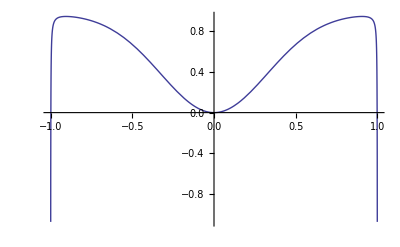

```mathematica
Plot[Inv[lv,ss,eq[[2]],xinv],{xinv,-1,1}]
```

### Commands work with more than one strategy

```mathematica
ss2=FindSingularStrategy[lv,{-0.4,0.4},{0.1,0.1}]
```

{x[1]→-0.314538,x[2]→0.314538}

```mathematica
eq2=FindEcoAttractor[lv,ss2,{0.1,0.1}]
```

{n[1]→0.811066,n[2]→0.811066}

```mathematica
ESSQ[lv,ss2,eq2]
```

{False,False}

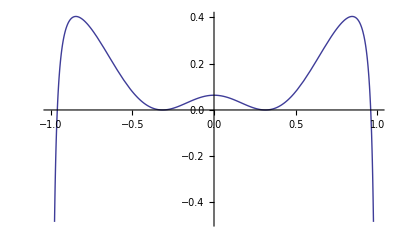

```mathematica
Plot[Inv[lv,ss2,eq2,xinv],{xinv,-1,1}]
```

### PIP and MIP plotting

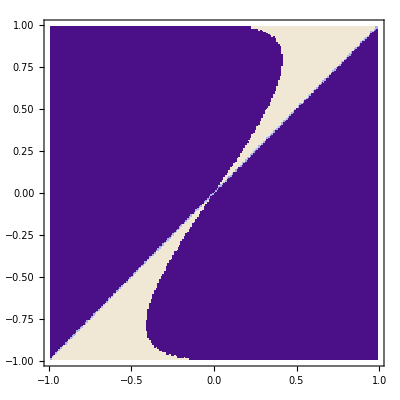

```mathematica
PlotPIP[lv,{-0.99,0.99,0.01},Output->True]
```

```mathematica
mip=PlotMIP[lv,{-0.99,0.99,0.01},Input->True]
```

-Graphics-

### Two kinds of evolutionary simulations - EcoEvoSim (population dynamics + canonical equation) and EvoSim (mutation-limited)

#### This is fun ... run an EcoEvoSim with two initially very similar species that will evolve together to a branching point, then split up

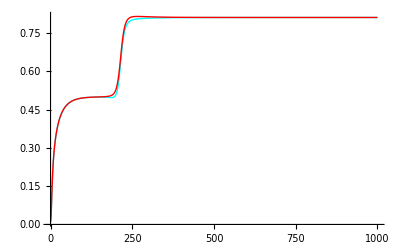

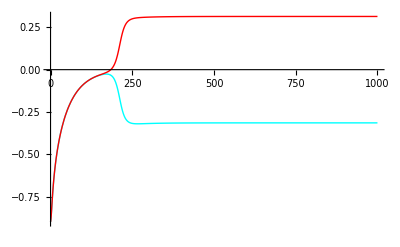

```mathematica
Clear[x];

tmax=1000;

nsp=2;
xi[1]=-0.9000001;
xi[2]=-0.9;

sol=EcoEvoSim[lv,Table[xi[i],{i,1,nsp}],Table[0.01,{i,1,nsp}],0.01,tmax];

Plot[Evaluate[Table[n[i][t],{i,1,nsp}]/.sol],{t,0,tmax},PlotStyle->Table[Hue[i/nsp],{i,1,nsp}],PlotRange->All]
Plot[Evaluate[Table[x[i][t],{i,1,nsp}]/.sol],{t,0,tmax},PlotStyle->Table[Hue[i/nsp],{i,1,nsp}],PlotRange->All]
```

```mathematica
dyn=ParametricPlot[{x[1][t],x[2][t]}/.sol,{t,0,tmax},PlotStyle->{Green,Thickness[0.012]}];

Show[mip,dyn,PlotRange->All,DisplayFunction->$DisplayFunction]
```

-Graphics-

### FindEvoAttractor finds a global ESS

```mathematica
ess=FindEvoAttractor[lv,{0.2}]
```

{-0.571372,-0.179012,0.179012,0.571372}

```mathematica
(* now let's plot the invasion function *)
```

```mathematica
eq=FindEcoEq[lv,ess,{1,1,1,1}]
```

{n[1]→0.432508,n[2]→0.513296,n[3]→0.513296,n[4]→0.432508}

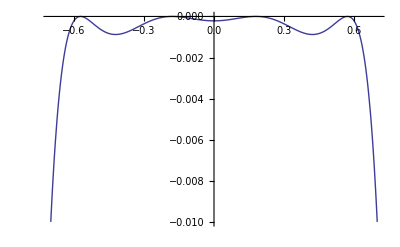

```mathematica
Plot[Inv[lv,ess,eq,xinv],{xinv,-0.7,0.7},PlotRange->{-0.01,0}]
```

### BifurcationData generates a bifurcation diagram of singular strategy (of a given number of species) versus a model parameter. By default, solid squares are global ESS's, open squares are local, but non-global ESS's, and dots are non-ESS's.

#### One species

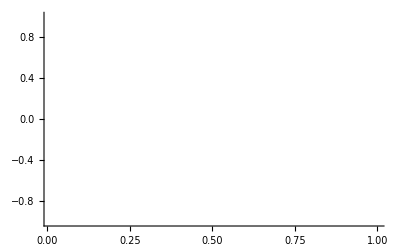

```mathematica
Clear[nsp,σa];
bd1=BifurcationData[lv,{σa,1.0,0.01,-0.01},{0.1}];bp1=PlotBifurcationData[bd1]
```

#### Two species

#### Since this is a numerical continuation, it is mandatory to start on the right track.

```mathematica
σa=0.7;
FindEvoAttractor[lv,{0.4,-0.4}]
Clear[σa];
```

{0.0812819,-0.0812819}

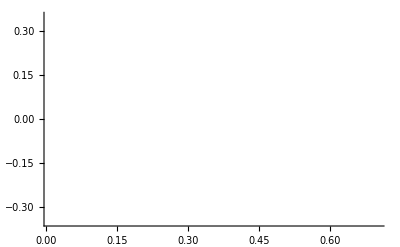

```mathematica
bd2=BifurcationData[lv,{σa,0.7,0.01,-0.01},{0.0812819,-0.0812819},FindSingularStrategyOpts->{FitnessGradientOpts->{Method->{"TwoPoint",0.001}}}];
bp2=PlotBifurcationData[bd2]
```

#### Three species

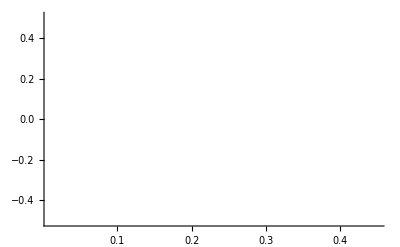

```mathematica
bd3=BifurcationData[lv,{σa,0.45,0.01,-0.01},{0.36,-0.36,0}];
bp3=PlotBifurcationData[bd3]
```

#### Four species

```mathematica
σa=0.34;
FindEvoAttractor[lv,{0.36,-0.36,0.01,-0.01}]
Clear[σa];
```

{0.506823,-0.506823,0.0604856,-0.0604856}

FindEcoAttractor::nosteq: Warning: no stable equilibrium with traits {0.574158, -0.574157, 0.428176, -0.428139}.  Resorting to numerical solution.

NIntegrate::inumr: The integrand 1 has evaluated to non-numerical values for all sampling points in the region with boundaries {{500., 505.886}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindEcoAttractor::nosteq: Warning: no stable equilibrium with traits {0.112761, -0.112761, 0.0370448, -0.0370448}.  Resorting to numerical solution.

FindEcoAttractor::nosteq: Warning: no stable equilibrium with traits {0.0649963, -0.0649963, 0.0214341, -0.0214341}.  Resorting to numerical solution.

General::stop: Further output of FindEcoAttractor :: nosteq will be suppressed during this calculation.

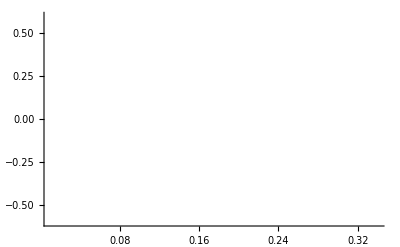

```mathematica
bd4=BifurcationData[lv,{σa,0.34,0.01,-0.01},{0.5068,-0.5068,0.0604,-0.0604},FindSingularStrategyOpts->{Method->"Newton"}];
bp4=PlotBifurcationData[bd4]
```

#### Putting them together

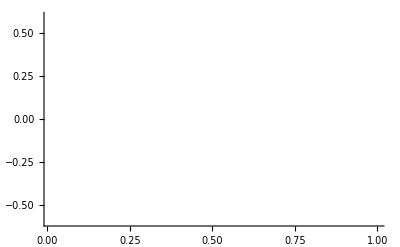

```mathematica
Show[bp1,bp2,bp3,bp4]
```

#### The transition from 2 to 3 species looks interesting. Let's zoom in. What's going on here?

These graphs show that the various levels of omega-a allow for the co-existence of multiple species and as the competition between species decreases, more species are able to stabily co-exist over evolutionary timespans.

```mathematica
(* WARNING - can take a long time/generates some error messages along the way *)
```

FindEcoAttractor::nosteq: Warning: no stable equilibrium with traits {0.346369, -0.346369, -4.54723×10^-15}.  Resorting to numerical solution.

NIntegrate::inumr: The integrand 1 has evaluated to non-numerical values for all sampling points in the region with boundaries {{500., 503.045}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.22871×10^-12 and 3.50371×10^-15 for the integral and error estimates.

FindEcoAttractor::nosteq: Warning: no stable equilibrium with traits {0.348367, -0.346369, -4.54723×10^-15}.  Resorting to numerical solution.

General::stop: Further output of FindEcoAttractor :: nosteq will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.6717×10^-15 and 5.00813×10^-15 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.15469×10^-13 and 3.96379×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

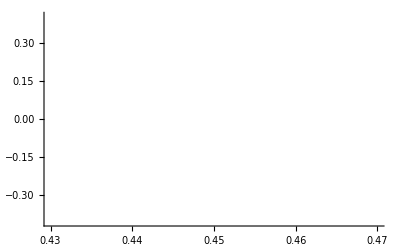

```mathematica
Clear[σa];
bd2=BifurcationData[lv,{σa,0.43,0.47,0.001},{0.35,-0.35}];bp2=PlotBifurcationData[bd2];
bd3=BifurcationData[lv,{σa,0.43,0.47,0.001},{0.35,-0.35,0}];bp3=PlotBifurcationData[bd3,SymbolShape->{PlotSymbol[Triangle,4],PlotSymbol[Triangle,4,Filled->False],PlotSymbol[Triangle,1]}];
Show[bp2,bp3]
```

### FindBranchingPoint locates the parameter value where a singular strategy changes ESS stability

```mathematica
Clear[σa];
FindBranchingPoint[lv,{σa,1.1},{0.1}]
```

0.707107

```mathematica
FindBranchingPoint[lv,{σa,0.5},{0.4,-0.4}]
```

0.441035